# Plasma emission

## blackbody plot

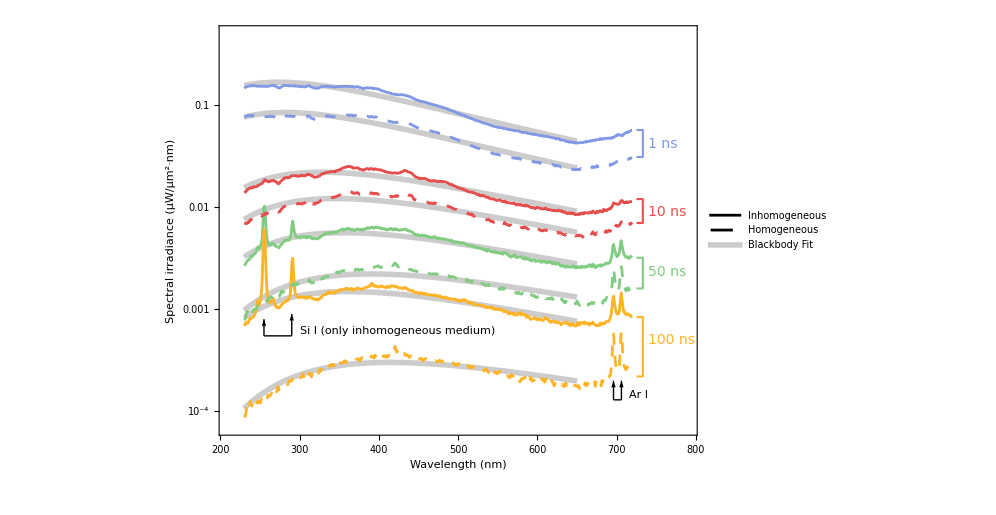

```mathematica
(* -- import data -- *)
dt=Import[NotebookDirectory[]<>"data/continuum/core.mx"];
fdt=Import[NotebookDirectory[]<>"data/continuum/"<>"coreFitData.mx"];

(* -- plot style -- *)
clr={RGBColor[.5,.6,.9],RGBColor[.9,.3,.3],RGBColor[.5,.8,.5],RGBColor[1,.7,.15]};
ps=Directive@@@Flatten[{
ConstantArray[{RGBColor[.8,.8,.8,1],AbsoluteThickness[4]},8],
{#,AbsoluteThickness[2]}&/@clr,
{#,AbsoluteThickness[2],AbsoluteDashing[8]}&/@clr
},1];

(* -- plot -- *)
idx={1,3,5,6};
gf=ListLinePlot[

Flatten[{fdt[[1,idx]],fdt[[2,idx]],dt[[1,idx,;;;;4]],dt[[2,idx,;;;;4]]},1],

Epilog->{
(* -- delay time label -- *)
{{clr[[1]],AbsoluteThickness[1.5],Line[{{725,Log@.057},{733,Log@.057},{733,Log@.031},{725,Log@.031}}]},
Text[Style["1 ns",{FontColor->clr[[1]],FontSize->14,FontWeight->Plain}],{740,Log@.042},{-1,0}]},
{{clr[[2]],AbsoluteThickness[1.5],Line[{{725,Log@.012},{733,Log@.012},{733,Log@.0070},{725,Log@.0070}}]},
Text[Style["10 ns",{FontColor->clr[[2]],FontSize->14,FontWeight->Plain}],{740,Log@.009},{-1,0}]},
{{clr[[3]],AbsoluteThickness[1.5],Line[{{725,Log@.0032},{733,Log@.0032},{733,Log@.0016},{725,Log@.0016}}]},
Text[Style["50 ns",{FontColor->clr[[3]],FontSize->14,FontWeight->Plain}],{740,Log@.0023},{-1,0}]},
{{clr[[4]],AbsoluteThickness[1.5],Line[{{725,Log@.00084},{733,Log@.00084},{733,Log@.00022},{725,Log@.00022}}]},
Text[Style["100 ns",{FontColor->clr[[4]],FontSize->14,FontWeight->Plain}],{740,Log@.0005},{-1,0}]},
(* -- Si I lines -- *)
{Black,AbsoluteThickness[1],Arrowheads[.02],Arrow[{{255,Log@.00055},{255,Log@.0008}}]},
{Black,AbsoluteThickness[1],Line[{{255,Log@.00055},{290,Log@.00055}}]},
{Black,AbsoluteThickness[1],Arrowheads[.02],Arrow[{{290,Log@.00055},{290,Log@.0009}}]},
{FontSize->14,Text["Si I (only inhomogeneous medium)",{300,Log@.00055},{-1,-1}]},
(* -- Ar I lines -- *)
{Black,AbsoluteThickness[1],Arrowheads[.02],Arrow[{{696,Log@.00013},{696,Log@.0002}}]},
{Black,AbsoluteThickness[1],Line[{{696,Log@.00013},{706,Log@.00013}}]},
{Black,AbsoluteThickness[1],Arrowheads[.02],Arrow[{{706,Log@.00013},{706,Log@.0002}}]},
{FontSize->14,Text["Ar I",{716,Log@.00013},{-1,-1}]}
},

PlotRange->{{210,790},{7*^-5,.5}},
Joined->True,
ScalingFunctions->{"Linear","Log"},

PlotStyle->ps,

PlotLegends->
Placed[
LineLegend[
{Directive[Black,AbsoluteThickness[2]],Directive[Black,AbsoluteThickness[2],AbsoluteDashing[8]],Directive[RGBColor[.8,.8,.8,1],AbsoluteThickness[4]]},
{"Inhomogeneous","Homogeneous","Blackbody Fit"},
LegendMarkerSize->{{60,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->{"Row",1}
],
{{.5,.96},{.5,1}}],

Axes->False,
Frame->True,
FrameLabel->{{"Spectral irradiance (μW/μm^2·nm)",None},{"Wavelength (nm)",None}},
FrameTicks->{
{Table[{i,If[FractionalPart[Log10@i]==0,Superscript[10,IntegerPart@Log10[i]]],{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[10^-6,10.,10]}]}],Table[{i,Null,{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[10^-6,10.,10]}]}]},
{Table[{i,If[Mod[i,100]==0,i],{If[Mod[i,50]==0,.015,.008],0}},{i,200,800,10}],Table[{i,Null,{If[Mod[i,50]==0,.015,.008],0}},{i,200,800,10}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,
GridLinesStyle->{{Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},

PlotRangeClipping->False,
ImagePadding->{{55,5},{45,5}},
ImageSize->(130*2)*(72/25.4),AspectRatio->.7

];

Print[gf];

(* -- export -- *)
Export[NotebookDirectory[]<>"fit.pdf",gf];
```

## time dependence

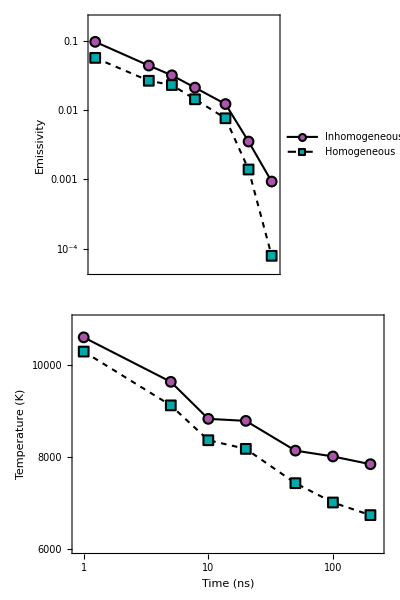

```mathematica
(* -- import data -- *)
raw=Import[NotebookDirectory[]<>"data/continuum/"<>"coreFitParameters.mx"];

t={1,5,10,20,50,100,200};
dtEmissivity={{t,raw[[1,All,1]]}ᵀ,{t,raw[[2,All,1]]}ᵀ};
dtTemperature={{t,raw[[1,All,2]]}ᵀ,{t,raw[[2,All,2]]}ᵀ};

(* -- plot -- *)
gfa=ListLinePlot[

dtEmissivity,

Epilog->{
(* panel label *)
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

PlotRange->{{.9,230},{5*^-5,.2}},
Joined->True,
ScalingFunctions->{"Log","Log"},

PlotStyle->{
Directive[Black,AbsoluteThickness[1.5]],
Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]
},

PlotMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},

PlotLegends->
Placed[
LineLegend[
{Directive[Black,AbsoluteThickness[1.5]],Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]},
{"Inhomogeneous","Homogeneous"},
LegendMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},
LegendMarkerSize->{{40,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->{"Column",1}
],
{{.03,.08},{0,0}}],

Axes->False,
Frame->True,
FrameLabel->{{"Emissivity",None},{None,None}},
FrameTicks->{
{Table[{i,If[FractionalPart[Log10@i]==0,Superscript[10,Log10[i]],Null],{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[10^-5,1,10]}]}],Table[{i,Null,{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[10^-5,1,10]}]}]},
{Table[{i,Null,{If[MemberQ[t,i],.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}],Table[{i,Null,{If[MemberQ[t,i],.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,
GridLinesStyle->{{Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},

PlotRangeClipping->False,
ImagePadding->{{70,5},{45,5}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.5

];

gfb=ListLinePlot[

dtTemperature,

Epilog->{
(*panel label*)
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

PlotRange->{{.9,230},{6000,11000}},
Joined->True,
ScalingFunctions->{"Log","Linear"},

PlotStyle->{
Directive[Black,AbsoluteThickness[1.5]],
Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]
},

PlotMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},

Axes->False,
Frame->True,
FrameLabel->{{"Temperature (K)",None},{"Time (ns)",None}},
FrameTicks->{
{Table[{i,If[Mod[i,2000]==0,i],{If[Mod[i,2000]==0,.015,.008],0}},{i,5000,12000,500}],Table[{i,Null,{If[Mod[i,2000]==0,.015,.008],0}},{i,5000,12000,500}]},
{Table[{i,If[MemberQ[t,i],i,Null],{If[MemberQ[t,i],.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}],Table[{i,Null,{If[MemberQ[t,i],.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,
GridLinesStyle->{{Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},

PlotRangeClipping->False,
ImagePadding->{{70,5},{45,5}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.5

];

gf=Grid[{{gfa},{gfb}},Spacings->0];
Print[gf];

Export[NotebookDirectory[]<>"temporal.pdf",gf];
```

## radial profile

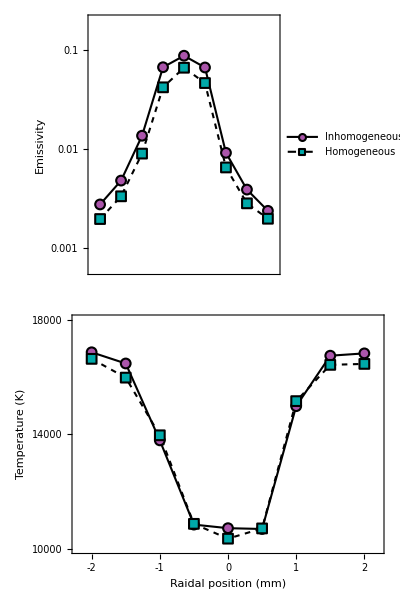

```mathematica
(* -- import data -- *)
raw=Import[NotebookDirectory[]<>"data/continuum/"<>"radialFitParameters.mx"];

z=Range[-2,2,.5];
dtEmissivity={{z,raw[[1,All,1]]}ᵀ,{z,raw[[2,All,1]]}ᵀ};
dtTemperature={{z,raw[[1,All,2]]}ᵀ,{z,raw[[2,All,2]]}ᵀ};

(* -- plot -- *)
gfa=ListLinePlot[

dtEmissivity,

Epilog->{
(* panel label *)
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

PlotRange->{{-2.2,2.2},{6*10^-4,.2}},
Joined->True,
ScalingFunctions->{"Linear","Log"},

PlotStyle->{
Directive[Black,AbsoluteThickness[1.5]],
Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]
},

PlotMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},

PlotLegends->
Placed[
LineLegend[
{Directive[Black,AbsoluteThickness[1.5]],Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]},
{"Inhomogeneous","Homogeneous"},
LegendMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},
LegendMarkerSize->{{40,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->{"Column",1}
],
{{.03,.92},{0,1}}],

Axes->False,
Frame->True,
FrameLabel->{{"Emissivity",None},{None,None}},
FrameTicks->{
{Table[{i,If[FractionalPart[Log10@i]==0,Superscript[10,Log10[i]],Null],{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[10^-5,1,10]}]}],Table[{i,Null,{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[10^-5,1,10]}]}]},
{Table[{i,Null,{If[FractionalPart[Mod[i,1]]==0,.015,.008],0}},{i,Range[-2,2,.25]}],Table[{i,Null,{If[FractionalPart[Mod[i,1]]==0,.015,.008],0}},{i,Range[-2,2,.25]}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,
GridLinesStyle->{{Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},

PlotRangeClipping->False,
ImagePadding->{{70,5},{45,5}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.5

];

gfb=ListLinePlot[

dtTemperature,

Epilog->{
(* panel label *)
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

PlotRange->{{-2.2,2.2},{10000,18000}},
Joined->True,
ScalingFunctions->{"Linear","Linear"},

PlotStyle->{
Directive[Black,AbsoluteThickness[1.5]],
Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]
},

PlotMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},

Axes->False,
Frame->True,
FrameTicks->{
{Table[{i,If[Mod[i-2000,4000]==0,i],{If[Mod[i-2000,4000]==0,.015,.008],0}},{i,10000,25000,1000}],Table[{i,Null,{If[Mod[i,5000]==0,.015,.008],0}},{i,10000,25000,1000}]},
{Table[{i,If[FractionalPart[Mod[i,1]]==0,IntegerPart@i,Null],{If[FractionalPart[Mod[i,1]]==0,.015,.008],0}},{i,Range[-2,2,.25]}],Table[{i,Null,{If[FractionalPart[Mod[i,1]]==0,.015,.008],0}},{i,Range[-2,2,.25]}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],
FrameLabel->{{"Temperature (K)",None},{"Raidal position (mm)",None}},
LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,
GridLinesStyle->{{Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},

PlotRangeClipping->False,
ImagePadding->{{70,5},{45,5}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.5

];

gf=Grid[{{gfa},{gfb}},Spacings->0];

Print[gf];

Export[NotebookDirectory[]<>"radial.pdf",gf];
```

## total radiation energy

ℰ_I ~ 1.2×10^-2 (mJ)

ℰ_H ~ 5.6×10^-3 (mJ)

ℰ_I/ℰ_H ~ 2.2

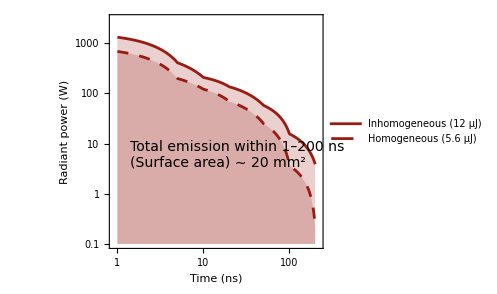

```mathematica
(* -- import data -- *)
raw=Import[NotebookDirectory[]<>"data/continuum/"<>"coreFitParameters.mx"];

t={1,5,10,20,50,100,200};
dtEmissivity={{t,raw[[1,All,1]]}ᵀ,{t,raw[[2,All,1]]}ᵀ};
dtTemperature={{t,raw[[1,All,2]]}ᵀ,{t,raw[[2,All,2]]}ᵀ};

(* -- interpolation -- *)
dtEmissivityFunc=Interpolation[#,InterpolationOrder->1]&/@dtEmissivity;
dtTemperatureFunc=Interpolation[#,InterpolationOrder->1]&/@dtTemperature;

(* -- Stefan-Bolzmann -- *)
σ=5.67*^-8;
area=2π(.001)^2+2π(.001)(.002);

powerInhomo[t_]:=σ area dtEmissivityFunc[[1]][t]*dtTemperatureFunc[[1]][t]^4;
powerHomo[t_]:=σ area dtEmissivityFunc[[2]][t]*dtTemperatureFunc[[2]][t]^4;
energyInhomo=NIntegrate[powerInhomo[t],{t,1,200}]*10^-9;
energyHomo=NIntegrate[powerHomo[t],{t,1,200}]*10^-9;

Print["ℰ_I ~ ",ScientificForm[energyInhomo*10^3,2]," (mJ)"];
Print["ℰ_H ~ ",ScientificForm[energyHomo*10^3,2]," (mJ)"];
Print["ℰ_I/ℰ_H ~ ",ScientificForm[energyInhomo/energyHomo,2]];

(* -- discrete data -- *)
dt={
Table[{t,powerInhomo[t]},{t,PowerRange[1,200,1.01]}],
Table[{t,powerHomo[t]},{t,PowerRange[1,200,1.01]}]
};

(* -- plot -- *)
gf=ListLinePlot[

dt,

Epilog->{
Text[Style["Total emission within 1–200 ns\n(Surface area) ∼ 20 mm^2",{FontColor->Black,FontSize->14,FontWeight->Plain,TextAlignment->Left}],Log@{1.4,3},{-1,-1}]
},

PlotRange->{{.9,220},{.1,3000}},
PlotRangePadding->0,
PlotRangeClipping->False,
ScalingFunctions->{"Log","Log"},

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

PlotStyle->{
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2],AbsoluteDashing[8]}
},

PlotLegends->Placed[
LineLegend[
{"Inhomogeneous (12 μJ)","Homogeneous (5.6 μJ)"},
LegendMarkerSize->{{30,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->"Column"],
{Scaled@({.08,.08}),{0,0}}],

Axes->False,
Frame->True,
FrameTicks->{
{Table[{i,If[FractionalPart[Log10@i]==0,Superscript[10,Log10[i]],Null],{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[.1,10^4,10]}]}],
Table[{i,Null,{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10.]},{n,PowerRange[.1,10^4,10]}]}]
},
{Table[{i,If[MemberQ[t,i],i,Null],{If[MemberQ[t,i],.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}],Table[{i,Null,{If[MemberQ[t,i],.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}]}
},
FrameLabel->{{"Radiant power (W)",None},{"Time (ns)",None}},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,

ImagePadding->{{50,10},{40,10}},
ImageSize->(65*2)*(72/25.4),
AspectRatio->.8,

Filling->{1->Bottom,2->Bottom}

];

Print[gf];

Export[NotebookDirectory[]<>"loss.pdf",gf];
```